1.26×10^12 x^2-2.52×10^15 x^3+1.26×10^18 x^4

0.0000238095

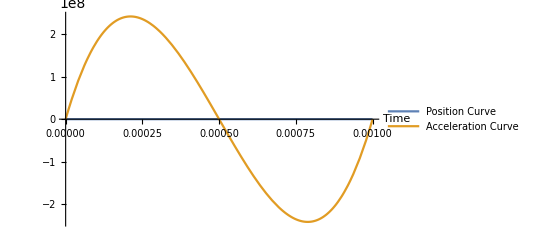

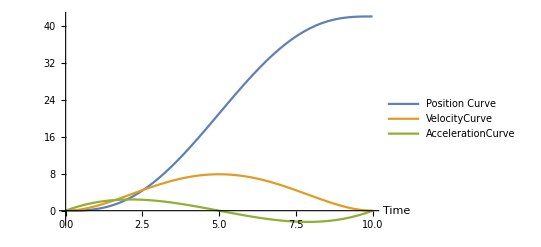

```mathematica
A0=0;
A1=0;
A2=0;
A3=0;
A4=0;
A5=0;
startAngle=0;
finalAngle=42;
startVelocity=0;
finalVelocity=0;
startAcceleration=0;
finalAcceleration=0;
overAllTime =0.001;
minSpeed = 0.1;
topSpeed =0.01;
A0=startAngle;
A1=startVelocity;
A2=startAcceleration/2;
A3=-1*(20*startAngle-20*finalAngle+12*overAllTime*startVelocity+8*overAllTime*finalVelocity+3*startAcceleration*overAllTime^2-finalAcceleration*overAllTime^2)/(2*overAllTime^3);
A4=(30*startAngle-30*finalAngle+16*overAllTime*startVelocity+14*overAllTime*finalVelocity+3*startAcceleration*overAllTime^2-2*finalAcceleration*overAllTime^2)/(2*overAllTime^4);
A5=-1*(12*startAngle-12*finalAngle+6*overAllTime*startVelocity+6*overAllTime*finalVelocity+startAcceleration*overAllTime^2-finalAcceleration*overAllTime^2)/(2*overAllTime^5);
PositionCurve[t_] :=  A5*t^5+A4*t^4+A3*t^3+A2*t^2+A1*t + A0;
VelocityCurve[t_] :=   PositionCurve'[t];
AccelerationCurve[t_] :=  PositionCurve''[t];
AccelerationCurve[x];
VelocityCurve[x]
eti = overAllTime/finalAngle

MotionGraph = Plot[{PositionCurve[x], AccelerationCurve[x]}, {x, 0, overAllTime}, PlotLegends->{"Position Curve", "Acceleration Curve"}, AxesLabel->{"Time"}]
```

```mathematica
timeDivisionSize =0.2;
timeDivisions = overAllTime / timeDivisionSize;
maxFuncValue = PolyFunction[(timeDivisions/2)*timeDivisionSize]
scalingCoef = (topSpeed-minSpeed)/maxFuncValue;
transformationFunction [input_] := scalingCoef*input+minSpeed;
For[i=0,i≤overAllTime,i+=timeDivisionSize,
Print[i];
Print[transformationFunction[ PolyFunction[i]]];
]
```

16.4063

0

0.1

0.2

0.0998589

0.4

0.0994468

0.6

0.0987806

0.8

0.0978766

1.

0.096751

1.2

0.0954194

1.4

0.0938973

1.6

0.0921996

1.8

0.090341

2.

0.088336

2.2

0.0861984

2.4

0.083942

2.6

0.0815801

2.8

0.0791255

3.

0.076591

3.2

0.0739888

3.4

0.0713307

3.6

0.0686285

3.8

0.0658933

4.

0.063136

4.2

0.0603672

4.4

0.057597

4.6

0.0548352

4.8

0.0520915

5.

0.049375

5.2

0.0466944

5.4

0.0440583

5.6

0.0414747

5.8

0.0389515

6.

0.036496

6.2

0.0341154

6.4

0.0318163

6.6

0.0296053

6.8

0.0274883

7.

0.025471

7.2

0.0235588

7.4

0.0217567

7.6

0.0200694

7.8

0.0185012

8.

0.017056

8.2

0.0157375

8.4

0.014549

8.6

0.0134934

8.8

0.0125733

9.

0.011791

9.2

0.0111483

9.4

0.0106468

9.6

0.0102878

9.8

0.010072

10.

0.01

10.2

0.010072

10.4

0.0102878

10.6

0.0106468

10.8

0.0111483

11.

0.011791

11.2

0.0125733

11.4

0.0134934

11.6

0.014549

11.8

0.0157375

12.

0.017056

12.2

0.0185012

12.4

0.0200694

12.6

0.0217567

12.8

0.0235588

13.

0.025471

13.2

0.0274883

13.4

0.0296053

13.6

0.0318163

13.8

0.0341154

14.

0.036496

14.2

0.0389515

14.4

0.0414747

14.6

0.0440583

14.8

0.0466944

15.

0.049375

15.2

0.0520915

15.4

0.0548352

15.6

0.057597

15.8

0.0603672

16.

0.063136

16.2

0.0658933

16.4

0.0686285

16.6

0.0713307

16.8

0.0739888

17.

0.076591

17.2

0.0791255

17.4

0.0815801

17.6

0.083942

17.8

0.0861984

18.

0.088336

18.2

0.090341

18.4

0.0921996

18.6

0.0938973

18.8

0.0954194

19.

0.096751

19.2

0.0978766

19.4

0.0987806

19.6

0.0994468

19.8

0.0998589

20.

0.1